```mathematica
<<coproduct.m
```

```mathematica
loadMPL5E[7]
```

HPL identities for letters {0,1} loaded through weight 7

Get::noopen: Cannot open TraditionalForm`"weight_7_irreducible_GI_functions.mx".

Get::noopen: Cannot open TraditionalForm`"weight_7_irreducible_GII_functions.mx".

MPL identities for letters {0,1,1/yu,1/yv,1/(yu*yv)} loaded through weight 7

```mathematica
loadLimits[DS,8]
```

Double Scaling limits loaded through weight 8

```mathematica
ClearAll[evaluate]
evaluate[funcName_,expression_,vars_,points_,ID_:1]:=Monitor[Module[{formattedExpression,expressionFile,pointsFile,outputFile,flagFile,count=0},
initializing="writing expression to file";
expressionFile=StringJoin["/Users/thatscottishkid/Google Drive/Stanford/Lance/Mathematica Library/ginac/expression_",ToString[ID],".dat"];
pointsFile=StringJoin["/Users/thatscottishkid/Google Drive/Stanford/Lance/Mathematica Library/ginac/points_",ToString[ID],".csv"];
flagFile=StringJoin["/Users/thatscottishkid/Google Drive/Stanford/Lance/Mathematica Library/ginac/done_",ToString[ID],".txt"];
formattedExpression=Expand[expression/.Table[vars[[ii]]->Evaluate[Symbol["var"<>ToString[ii]]],{ii,Length[vars]}]/.Zeta[a_]:>ζ[a]/.ζ[a__]:>zeta[a]];
Export[expressionFile,formattedExpression];
Export[pointsFile,points];
Export[StringJoin["/Users/thatscottishkid/Google\ Drive/Stanford/Lance/Mathematica\ Library/ginac/start_",ToString[ID],".txt"],ToString[funcName]];
While[!FileExistsQ[flagFile],initializing=StringJoin["waiting for ginac: ",ToString[count]," seconds"];count +=1;Pause[1]];
Get[flagFile];
DeleteFile[flagFile];
Get[outputFileName];
],initializing]
```

```mathematica
irreducibleDoubleScalingFunctionsToG={DS3[a_]:>irrToDSG[DS3[a]],DS4[a_]:>irrToDSG[DS4[a]],DS5[a_]:>irrToDSG[DS5[a]],DS6[a_]:>irrToDSG[DS6[a]],DS7[a_]:>irrToDSG[DS7[a]],DS8[a_]:>irrToDSG[DS8[a]]};
coproductDG[func_,var_]:=coproduct[{transcendentalWeight[func]-1,1},func]/.CircleDot[a_,b_]:>Apart[Expand[a*D[b/.toLogs,var]],var]
IntegrateG[func_,{var_,0,ul_}]:=Module[{replaceVar=(Reduce[var==ΩΩΩ]/.Equal[a_,b_]:>Rule[a,b]),integrand,improperArgs},
integrand=Apart[toLinearBasisG[Expand[func]]/.replaceVar,ΩΩΩ];
improperArgs=Select[DeleteCases[DeleteDuplicates[Flatten[Reap[integrand/.G[_,a_]:>Sow[a]]⟦2⟧]],ΩΩΩ],!FreeQ[#,ΩΩΩ]&];
If[Length[improperArgs]>0,Print["Multiple Polylogs of argument "<>ToString[improperArgs/.ΩΩΩ->var,InputForm]<>" present. Symbolic cannot be carried out on these terms."]];
Expand[Expand[integrand]/.
{G[aVec_,ΩΩΩ]/ΩΩΩ:>G[Prepend[aVec,0],temp],G[aVec_,ΩΩΩ]/Plus[ΩΩΩ,a__]:>G[Prepend[aVec,-Plus[a]],temp],Power[ΩΩΩ,-1]:>G[{0},temp],Power[Plus[ΩΩΩ,a__],-1]:>(G[{-a},temp]+G[{1},1+a])}/.temp->ul]];
toDSGc[func_]:=toDSGc[func]=Module[{functionalForm,integrationConst},
functionalForm=IntegrateG[-coproductDG[func,w]/.irreducibleDoubleScalingFunctionsToG,{1-w,0,1-w}];
integrationConst=IntegrateG[Expand[coproductDG[functionalForm,u]-coproductDG[func,u]]/.irreducibleDoubleScalingFunctionsToG,{1-u,0,1-u}];
Expand[(functionalForm+integrationConst- Expand[(functionalForm-integrationConst)/.u->1/.w->1])/.G->GredL]];
```

```mathematica
hexagonFunctions=Alternatives[H3[_],H4[_],H5[_],H6[_],E7[_],O7[_],E8[_],O8[_]];
```

```mathematica
toDSG:={func_:>Expand[func/.irreducibleDoubleScalingFunctionsToG/.flipArgument[{1-v,u,w}]/.{HPL[{___,1},v]->0,HPL[{0},v]->Log[v]}/.HPLtoG]/;FreeQ[func,hexagonFunctions]∧FreeQ[func,CircleDot]}
```

```mathematica
flipArgumentG[{x1_,xn___}]:=Join@@Table[flipArgumentG[i],{i,List[x1,xn]}]
flipArgumentG[var_]:={G[aVec_,var]:>Expand[IMPL[1-var,1-aVec,1]/.IMPLtoG]}
```

```mathematica
Get["physical_double_scaling_limits.dat"];
```

```mathematica
Get["weight_3_irreducible_DSG_functions.dat"];
Get["weight_4_irreducible_DSG_functions.dat"];
Get["weight_5_irreducible_DSG_functions.dat"];
Get["weight_6_irreducible_DSG_functions.dat"];
Get["weight_7_irreducible_DSG_functions.dat"];
```

```mathematica
CDSinner[weight_]:=CDSinner[weight]=Expand[Expand[Expand[toSurfaceE[V6[weight][v,w,u],v->0]+(toSurfaceE[V6[weight][v,w,u],v->0]/.exchange[u,w])+toSurfaceE[Vt6[weight][v,w,u],v->0]-(-toSurfaceE[Vt6[weight][v,w,u],v->0]/.exchange[u,w])]/.MPLtoHPL/.toDSG]/.G->GredL];
```

```mathematica
CDSouterI[weight_]:=CDSouterI[weight]=Expand[Expand[Expand[toSurfaceE[V6[weight][v,w,u],v->0]+(toSurfaceE[V6[weight][v,w,u],v->0]/.exchange[u,w])+toSurfaceE[Vt6[weight][v,w,u],v->0]-(-toSurfaceE[Vt6[weight][v,w,u],v->0]/.exchange[u,w])]/.MPLtoHPL/.toDSG]/.G->GredL/.(G[a_,1-u]:>G[-a,u-1]/;!(Length[a]==1∧Count[a,0]==1))];
```

```mathematica
CDSouterII[weight_]:=CDSouterII[weight]=Expand[Expand[Expand[toSurfaceE[V6[weight][v,w,u],v->0]+(toSurfaceE[V6[weight][v,w,u],v->0]/.exchange[u,w])+toSurfaceE[Vt6[weight][v,w,u],v->0]-(-toSurfaceE[Vt6[weight][v,w,u],v->0]/.exchange[u,w])]/.MPLtoHPL/.toDSG]/.G->GredL/.(G[a_,b_]:>G[-a,-b]/;!(Length[a]==1∧Count[a,0]==1))];
```

```mathematica
CDSouterIII[weight_]:=CDSouterIII[weight]=Expand[Expand[Expand[toSurfaceE[V6[weight][v,w,u],v->0]+(toSurfaceE[V6[weight][v,w,u],v->0]/.exchange[u,w])+toSurfaceE[Vt6[weight][v,w,u],v->0]-(-toSurfaceE[Vt6[weight][v,w,u],v->0]/.exchange[u,w])]/.MPLtoHPL/.toDSG]/.G->GredL/.(G[a_,1-w]:>G[-a,w-1]/;!(Length[a]==1∧Count[a,0]==1))];
```

```mathematica
innerPoints=Join[{{99/100,99/100},{1/100,999/1000},{999/1000,1/100}},
Flatten[Table[{u/10,1-u/10}+Power[10,-jj],{u,9},{jj,2,6}],1],
Table[{ii/10,99/100},{ii,9}],
Table[{99/100,ii/10},{ii,9}],
Select[Flatten[Table[{ii/10,jj/10},{ii,9},{jj,9}],1],#⟦1⟧+#⟦2⟧>1&]];
```

```mathematica
outerPointsI=Join[{{101/100,99/100},{101/100,1/100}},
Table[{101/100,ii/10},{ii,9}],
Table[{2^ii,99/100},{ii,20}],
Flatten[Table[{2^ii,jj/10},{ii,20},{jj,9}],1],
Flatten[Table[{2^ii,Power[10,-jj]},{ii,20},{jj,6}],1]];
```

```mathematica
outerPointsIII=Join[{{99/100,101/100},{1/100,101/100}},
Table[{ii/10,101/100},{ii,9}],
Table[{99/100,2^ii},{ii,20}],
Flatten[Table[{jj/10,2^ii},{ii,20},{jj,9}],1],
Flatten[Table[{Power[10,-jj],2^ii},{ii,20},{jj,6}],1]];
```

```mathematica
outerPointsII=Select[Join[{{101/100,101/100}},
Table[{101/100,2^ii},{ii,20}],
Table[{2^ii,101/100},{ii,20}],
Flatten[Table[{2^ii,2^jj},{ii,20},{jj,20}],1]],#⟦1⟧≥#⟦2⟧&];
```

```mathematica
evaluateNMHVpositivityDS[name_,loops_,logs_]:=Module[{},
evaluate[name,Coefficient[CDSinner[loops],Log[v],logs],{u,w},innerPoints,3];
evaluate[name,Coefficient[CDSouterI[loops],Log[v],logs],{u,w},outerPointsI,3];
evaluate[name,Coefficient[CDSouterII[loops],Log[v],logs],{u,w},outerPointsII,3];
evaluate[name,Coefficient[CDSouterIII[loops],Log[v],logs],{u,w},outerPointsIII,3]];
```

```mathematica
ClearAll[C1DSln0v]
evaluateNMHVpositivityDS[C1DSln0v,1,0]
```

```mathematica
ListPlot3D[Table[{point⟦1⟧,point⟦2⟧,Re[C1DSln0v@@point]},{point,Select[Join[innerPoints,outerPointsI,outerPointsII,outerPointsIII],Max@@#<10&]}],PlotRange->{0,-20}]
ListPlot3D[Join[Table[{Log10[point⟦1⟧],Log10[point⟦2⟧],Re[C1DSln0v@@point]},{point,Join[innerPoints,outerPointsI,outerPointsII,outerPointsIII]}],Table[{Log10[0.5+u/10],Log10[0.5-u/10],0},{u,-4,4}],Table[{0,-ii,0},{ii,6}],Table[{-ii,0,0},{ii,6}]],PlotRange->{-20,0.01},Ticks->{Transpose[{FindDivisions[{Log[10,.00001],Log[10,100000]},5],10^FindDivisions[{Log[10,.00001],Log[10,100000]},5]}],Transpose[{FindDivisions[{Log[10,.00001],Log[10,100000]},5],10^FindDivisions[{Log[10,.00001],Log[10,100000]},5]}],Automatic}]
```

-Graphics3D-

-Graphics3D-

```mathematica
ClearAll[C2DSln1v]
evaluateNMHVpositivityDS[C2DSln1v,2,1]
```

```mathematica
ListPlot3D[Table[{point⟦1⟧,point⟦2⟧,Re[C2DSln1v@@point]},{point,Select[Join[innerPoints,outerPointsI,outerPointsII,outerPointsIII],Max@@#<10&]}],PlotRange->All]
ListPlot3D[Join[Table[{Log10[point⟦1⟧],Log10[point⟦2⟧],Re[C2DSln1v@@point]},{point,Join[innerPoints,outerPointsI,outerPointsII,outerPointsIII]}],Table[{Log10[0.5+u/10],Log10[0.5-u/10],0},{u,-4,4}],Table[{0,-ii,0},{ii,6}],Table[{-ii,0,0},{ii,6}]],PlotRange->All,Ticks->{Transpose[{FindDivisions[{Log[10,.00001],Log[10,100000]},5],10^FindDivisions[{Log[10,.00001],Log[10,100000]},5]}],Transpose[{FindDivisions[{Log[10,.00001],Log[10,100000]},5],10^FindDivisions[{Log[10,.00001],Log[10,100000]},5]}],Automatic}]
```

-Graphics3D-

-Graphics3D-

```mathematica
ClearAll[C2DSln0v]
evaluateNMHVpositivityDS[C2DSln0v,2,0]
```

```mathematica
ListPlot3D[Table[{point⟦1⟧,point⟦2⟧,Re[C2DSln0v@@point]},{point,Select[Join[innerPoints,outerPointsI,outerPointsII,outerPointsIII],Max@@#<10&]}],PlotRange->All]
ListPlot3D[Join[Table[{Log10[point⟦1⟧],Log10[point⟦2⟧],Re[C2DSln0v@@point]},{point,Join[innerPoints,outerPointsI,outerPointsII,outerPointsIII]}],Table[{Log10[0.5+u/10],Log10[0.5-u/10],0},{u,-4,4}],Table[{0,-ii,0},{ii,6}],Table[{-ii,0,0},{ii,6}]],PlotRange->{0,50},Ticks->{Transpose[{FindDivisions[{Log[10,.00001],Log[10,100000]},5],10^FindDivisions[{Log[10,.00001],Log[10,100000]},5]}],Transpose[{FindDivisions[{Log[10,.00001],Log[10,100000]},5],10^FindDivisions[{Log[10,.00001],Log[10,100000]},5]}],Automatic}]
```

-Graphics3D-

-Graphics3D-

```mathematica
ClearAll[C3DSln2v]
evaluateNMHVpositivityDS[C3DSln2v,3,2]
```

```mathematica
ListPlot3D[Table[{point⟦1⟧,point⟦2⟧,Re[C3DSln2v@@point]},{point,Select[Join[innerPoints,outerPointsI,outerPointsII,outerPointsIII],Max@@#<3&]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[{point⟦1⟧,point⟦2⟧,Re[C3DSln2v@@point]},{point,Select[Join[innerPoints,outerPointsI,outerPointsII,outerPointsIII],Max@@#<10&]}],PlotRange->All]
ListPointPlot3D[Join[Table[{Log10[point⟦1⟧],Log10[point⟦2⟧],Re[C3DSln2v@@point]},{point,Join[innerPoints,outerPointsI,outerPointsII,outerPointsIII]}],Table[{Log10[0.5+u/10],Log10[0.5-u/10],0},{u,-4,4}],Table[{0,-ii,0},{ii,6}],Table[{-ii,0,0},{ii,6}]],PlotRange->{0.001,-20},Ticks->{Transpose[{FindDivisions[{Log[10,.00001],Log[10,100000]},5],10^FindDivisions[{Log[10,.00001],Log[10,100000]},5]}],Transpose[{FindDivisions[{Log[10,.00001],Log[10,100000]},5],10^FindDivisions[{Log[10,.00001],Log[10,100000]},5]}],Automatic}]
```

-Graphics3D-

-Graphics3D-

```mathematica
ClearAll[C3DSln1v]
evaluateNMHVpositivityDS[C3DSln1v,3,1]
```

```mathematica
ClearAll[C3DSln0v]
evaluateNMHVpositivityDS[C3DSln1v,3,0]
```

$Aborted

```mathematica
evaluate[C3DSln0v,Coefficient[CDSouterIII[3],Log[v],0],{u,w},outerPointsIII,4]
```

$Aborted

```mathematica
evaluate[C3DSln0v,Coefficient[CDSouterII[3],Log[v],0],{u,w},outerPointsII,4]
```

```mathematica
Return[]
```

```mathematica
Return[]
```

```mathematica
Table[{point,C1DSln0v[point,point]},{point,Sort[DeleteDuplicates[Flatten[Select[innerPoints,#⟦1⟧==#⟦2⟧&]]]]}]
```

(500001/1000000 | C1DSln0v(500001/1000000,500001/1000000)
50001/100000 | C1DSln0v(50001/100000,50001/100000)
5001/10000 | C1DSln0v(5001/10000,5001/10000)
501/1000 | C1DSln0v(501/1000,501/1000)
51/100 | C1DSln0v(51/100,51/100)
3/5 | C1DSln0v(3/5,3/5)
7/10 | C1DSln0v(7/10,7/10)
4/5 | C1DSln0v(4/5,4/5)
9/10 | C1DSln0v(9/10,9/10)
99/100 | -1.62478283411718007)

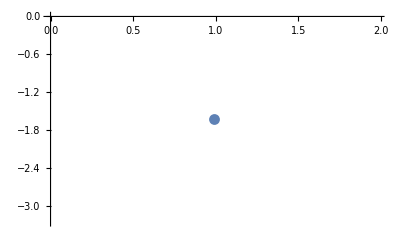

```mathematica
ListPlot[Table[{point,C1DSln0v[point,point]},{point,Sort[DeleteDuplicates[Flatten[Select[innerPoints,#⟦1⟧==#⟦2⟧&]]]]}]]
```